```mathematica
PDF[NormalDistribution[0,1],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
CDF[NormalDistribution[0,1],x]
```

1/2 (1+Erf[x/(√2)])

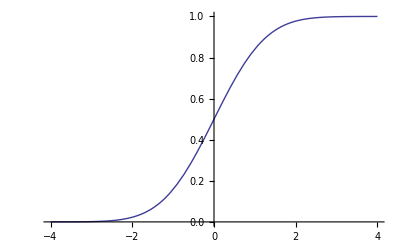

```mathematica
Plot[CDF[NormalDistribution[0,1],x],{x,-4,4}]
```

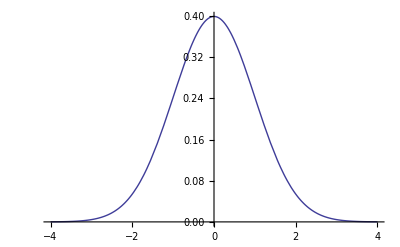

```mathematica
Plot[PDF[NormalDistribution[0,1],x],{x,-4,4}]
```

```mathematica
p1=RegionPlot[
y<PDF[NormalDistribution[0,1],x]&& 
-2 < x < 2,
{x,-4,4},
{y,0,0.4},
BoundaryStyle->Directive[Black],
PlotStyle->RGBColor[0.9,0.9,0.9]
];
p2=Plot[PDF[NormalDistribution[0,1],x],{x,-4,4}];
```

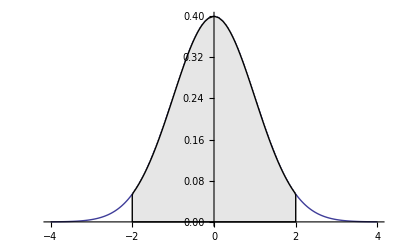

```mathematica
Show[p2,p1]
```

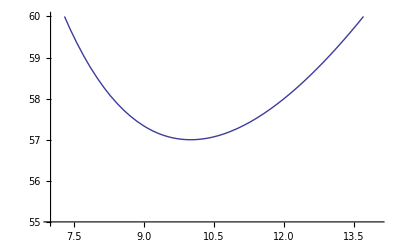

```mathematica
Plot[3b+300/b-3,{b,7,14}, PlotRange->{55,60}]
```

```mathematica
D[(3b+300/b-3), b]
```

3-300/b^2

```mathematica
Solve[D[(3b+300/b-3), b]==0,b]
```

{{b→-10},{b→10}}

```mathematica
3b+300/b-3/.{b->10}
```

57

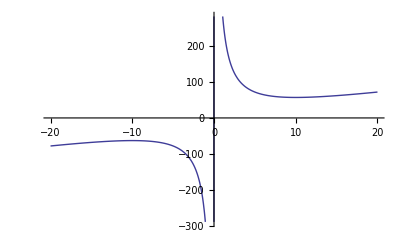

```mathematica
Plot[3b+300/b-3,{b,-20,20}]
```

```mathematica
o[g_]:=0.1 g^0.67
```

```mathematica
o[360 10^3]
```

528.108

```mathematica
Off[Solve::ifun]
```

```mathematica
Solve[o[g]==350,g]
```

{{g→194829.}}

```mathematica
g-150 10^3/.Solve[o[g]==350,g][[1]]
```

44829.1

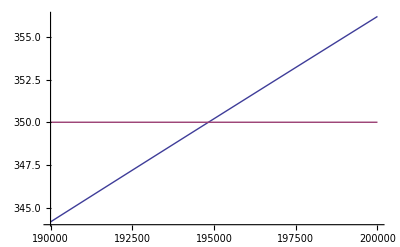

```mathematica
Plot[{o[g],350},{g,190 10^3,200 10^3}]
```

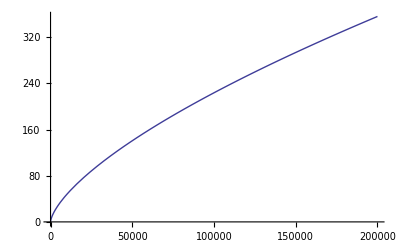

```mathematica
Plot[o[g],{g,0,200 10^3}]
```

```mathematica
Log[2]/Log[1.0225]
```

31.1518

```mathematica
p1=RegionPlot[
y<PDF[NormalDistribution[181,7],x]&& 
-∞ < x < 185,
{x,151,221},
{y,0,0.5},
BoundaryStyle->Directive[Black, Dashed],
PlotStyle->Directive[RGBColor[0.9,0.9,0.9]]
];
p2=Plot[
PDF[NormalDistribution[181,7],x],
{x,151,221},
PlotStyle->Directive[Black,Thickness[0.005]]
];
p3=Graphics[Style[Text["μ=181\nσ=7",{200,0.05}],12, FontFamily->"Helvetica"]];
```

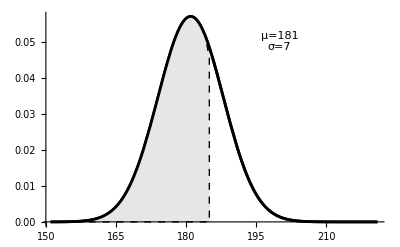

```mathematica
Show[p2,p1,p2, p3]
```